```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/implementation/"]
]
```

C:\Users\pwrzo\Documents\GitHub\AvoidedQP\implementation

```mathematica
getPlotData[qpds_]:=(
ks = Normal[DeleteDuplicates[qpds[Take,"momentum"]]];
kinds=PositionIndex[Normal[qpds[Take,"momentum"]]];
qpkds=Table[qpds[kinds[[it]]],{it,Length[kinds]}];
Bs=Normal[DeleteDuplicates[qpds[Take,"interaction"]]];
Binds=Table[PositionIndex[Normal[qpkds[[it]][Take,"interaction"]]],{it,Length[qpkds]}];

weightData=Table[
Table[(
qpSize=Normal[qpkds[[kt]][Take,"size"][Binds[[kt]][B]]];
qpWeight=Normal[qpkds[[kt]][Take,"weight"][Binds[[kt]][B]]];
Table[{1/qpSize[[it]],qpWeight[[it]]},{it,Length[qpSize]}]
),{B,Bs}],
{kt,Length[ks]}];
gapData=Table[
Table[(
qpSize=Normal[qpkds[[kt]][Take,"size"][Binds[[kt]][B]]];
qpWeight=Normal[qpkds[[kt]][Take,"gap"][Binds[[kt]][B]]];
Table[{1/qpSize[[it]],qpWeight[[it]]},{it,Length[qpSize]}]
),{B,Bs}],
{kt,Length[ks]}];
)
```

```mathematica
makeFits[qpds_,linePoints_,parabolaPoints_]:=(
getPlotData[qpds];
linear=Table[Table[
Fit[gapData[[kt,it,-Min[linePoints,Length[gapData[[kt,it]]]];;-1]],{1,x},x],
{it,1,Length[gapData[[kt]]]}],{kt,Length[ks]}];
quadratic=Table[Table[
Fit[weightData[[kt,it,-Min[parabolaPoints,Length[weightData[[kt,it]]]];;-1]],{1,x,x^2},x],
{it,1,Length[weightData[[kt]]]}],{kt,Length[ks]}];
{linear,quadratic})
```

```mathematica
makePlots[qpds_,fits_,J_]:=(
linear=fits[[1]];
quadratic=fits[[2]];
colors={Blue,Darker[Green],Orange,Red};
opacity={0.7,0.7};
pltStyle=Table[Directive[color,Opacity[opacity[[1]]]],{color,colors}];
parabolaStyle=Table[Directive[color,Opacity[opacity[[2]]]],{color,colors}];
lineStyle=Table[Directive[color,Dashed,Opacity[opacity[[2]]]],{color,colors}];
Table[(
line=linear[[kt]];
parabola=quadratic[[kt]];
{
Show[
ListPlot[
weightData[[kt]],
Frame->True,Axes->False,PlotMarkers->{"●",10},Joined->False,
FrameStyle->Directive[Black,18],
ImageSize->450,
PlotRange->{{0,0.1},{-0.01,0.5}},
FrameLabel->{Style["L^-1",Black,20,FontFamily->"Bookman Old Style"],Style["z",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,18],
PlotStyle->pltStyle,
PlotLegends->None,
PlotLabel->Style[StringJoin["J = ",J,"t   k = ",ToString[NumberForm[ks[[kt]],{2,1}]],"π"],Black,20,FontFamily->"Bookman Old Style"]
],
 Plot[line, {x, -0.2,-0.1},
PlotStyle->lineStyle
],
 Plot[parabola, {x, -0.2, 0.1},
PlotStyle->parabolaStyle
]
],
Show[
ListPlot[
gapData[[kt]],
Frame->True,Axes->False,PlotMarkers->{"●",10},Joined->False,
FrameStyle->Directive[Black,18],
ImageSize->450,
PlotRange->{{0,0.1},{-0.01,2.0}},
FrameLabel->{Style["L^-1",Black,20,FontFamily->"Bookman Old Style"],Style["ΔE",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,18],
PlotStyle->pltStyle,
PlotLegends->Table[StringJoin["β = ",ToString[NumberForm[B,{2,1}]]],{B,Bs}],
PlotLabel->Style[StringJoin["J = ",J,"t   k = ",ToString[NumberForm[ks[[kt]],{2,1}]],"π"],Black,20,FontFamily->"Bookman Old Style"]
],
 Plot[line, {x, -0.2,0.1},
PlotStyle->lineStyle
]
]
}
),
{kt,Length[ks]}]
)
```

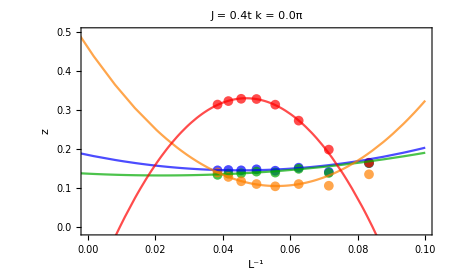
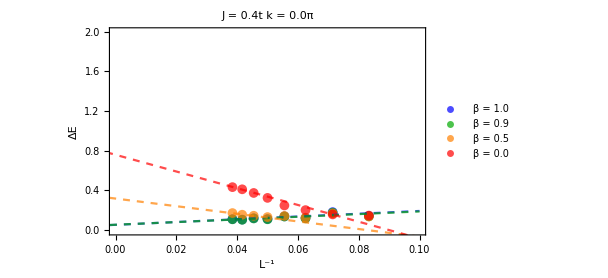
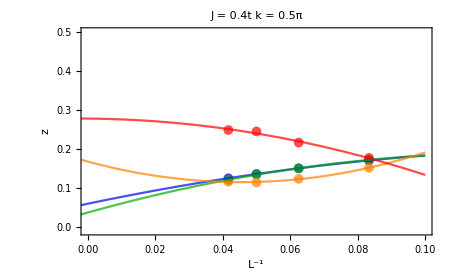
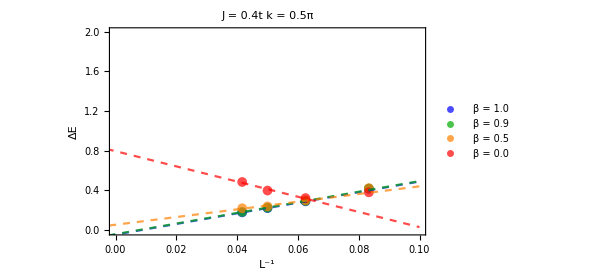
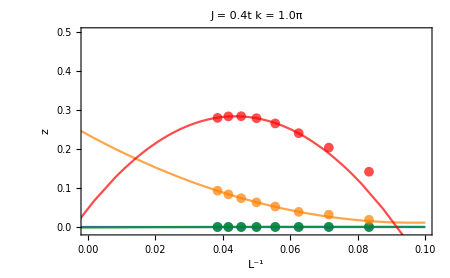
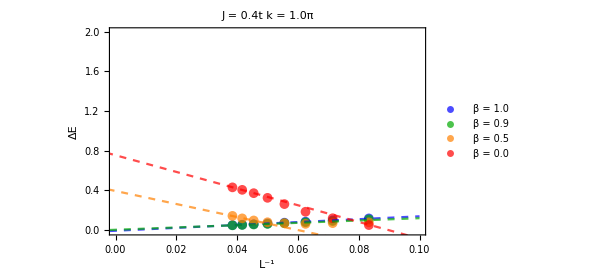
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

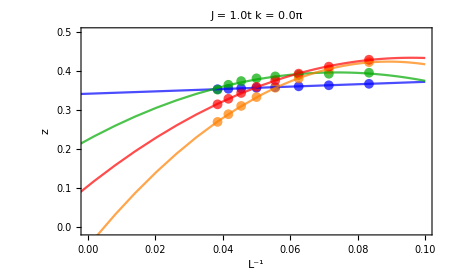
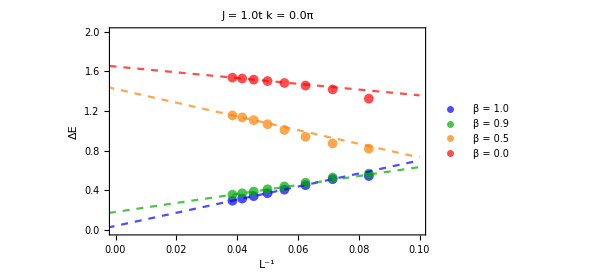
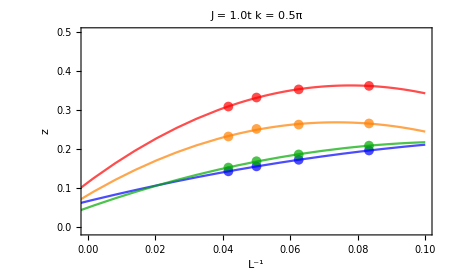
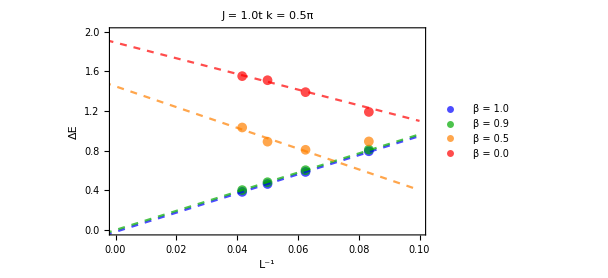
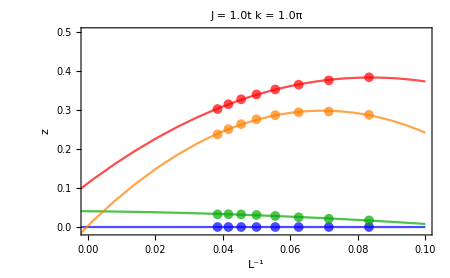
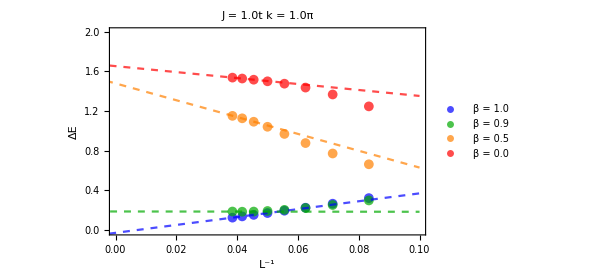
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
J={"0.4","1.0"};
linePoints={3,3};
parabolaPoints={6,8};

plots={};
qpds={};
fits={};
Do[(
qpData=Import[StringJoin["data/12-26_qp_J=",J[[iJ]],".json"],"RawJSON"];
AppendTo[qpds,Dataset[qpData]];
AppendTo[fits,makeFits[qpds[[-1]],linePoints[[iJ]],parabolaPoints[[iJ]]]];
AppendTo[plots,makePlots[qpds[[-1]],fits[[-1]],J[[iJ]]]];
),{iJ,Length[J]}]

qpg0=fits[[;;,1]]/.x->0;
qpw0=fits[[;;,2]]/.x->0;
dsw0=Table[
Dataset[Table[
Association[{"k [π]" ->ks[[kt]],"β"->Bs[[it]],"z(L^-1 → 0)"->qpw0[[id]][[kt]][[it]],"ΔE(L^-1 → 0)"->qpg0[[id]][[kt]][[it]]}],{kt,Length[ks]},{it,Length[Bs]}]],
{id,Length[qpw0]}];

qpds[[1]]
p1=Grid[plots[[1]],Spacings->{Automatic,2}]
w1=dsw0[[1]]

qpds[[2]]
p2=Grid[plots[[2]],Spacings->{Automatic,2}]
w2=dsw0[[2]]
```

```mathematica
(*
Export["mathematica/qp_J=0.4.pdf",p1]
Export["mathematica/qp_J=1.0.pdf",p2]
Export["mathematica/w0_J=0.4.pdf",w1]
Export["mathematica/w0_J=1.0.pdf",w2]
*)
```